```mathematica
E0 = 2;
m = 250;
n = 250;
A = Table[0, {m}, {n}];
B = Table[0, {m}, {n}];
A[[1, 1]] = 1/2;
B[[1, 1]] = 1/2;
For [k = 1, k <= m, k++,
 For [j = 1, j <= n, j++,p = k - 1;q = j - 1;
  Which[k == 1 && j > 1,
   					A[[1, j]] = (1/((2 q)*(2 q - 1)))*A[[1, j - 1]];
   					B[[1, j]] = (1/((2*q)*((2*q) + 1)))*B[[1, j - 1]],
   	   k > 1 && j == 1,
   					A[[k, 1]] = (+1)(1/(((E0 + 2)*p)*(((E0 + 2)*p) - 1)))*A[[k - 1, 1]];
   					B[[k, 1]] = (+1)(1/((1 + (E0 + 2)*p)*(((E0 + 2)*p))))*B[[k - 1, 1]],
                k > 1 && j > 1,
   					A[[k, 
     j]] = (1/(((E0 + 2)*p + 2*q)*(((E0 + 2)*p) + 2*q - 1)))*((+1)*A[[k - 1, j]] + 
       A[[k, j - 1]]);
   				           
   B[[k, j]] = (1/((1 + (E0 + 2)*p + 2*q)*(((E0 + 2)*p) + 2*q)))*((+1)*B[[k - 1, 
        j]] + B[[k, j - 1]])];
  ]
 ]
```

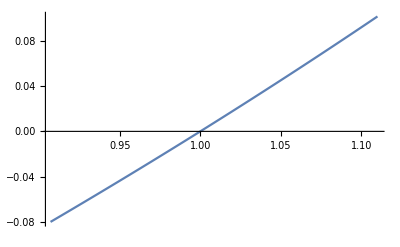

InterpolatingFunction[{{0.907, 1.11}}, <>]

```mathematica
r = 8;
Teta =  -(1/2)*((E0 - 2)/(E0 + 2))*Pi;
Z = r*Exp[I*Teta];
z = I*Z;
Eg = 1.11;
dx = .007;
sp0=.90;
sp=sp0 + dx;
L = (Eg-sp0)/dx;
h = 0;
Sy1 = Table[1, {L}];
Sy2 = Table[1, {L}];
c = Table[1, {L}];
For[l = sp, l <= Eg, l = l + dx,
 h = h + 1;
 For [k = 1, k <= m, k++,
  For [j = 1, j <= n, j++,
   p = k - 1;
   q = j - 1;
                  Sy1[[h]] = Sy1[[h]] + A[[k, j]]*((z)^((E0 + 2)*p + (2*q)))*(l^q);
                  Sy2[[h]] = Sy2[[h]] + B[[k, j]]*((z)^(1 + (E0 + 2)*p + (2*q)))*(l^q);
   ]
  ];
  c[[h]] = -Sy1[[h]]/Sy2[[h]];
 ]

StepE=Table[i, {i,sp, Eg,dx}];
dots=Transpose[{StepE,-Im[c]}];
ListLinePlot[dots]
iFun=Interpolation[dots]
```

```mathematica
s$rule=FindRoot[iFun[x],{x, 1},WorkingPrecision->20];
x$sol=x/.s$rule
```

1.0000000000872588809

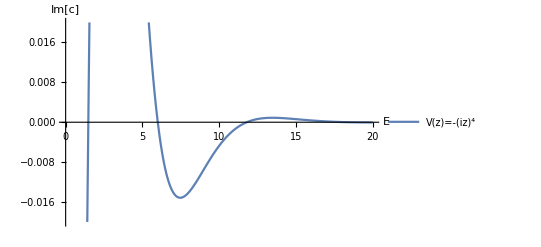

NmX4.jpg

/home/nhassanpour

InterpolatingFunction[{{0.1, 20.}}, <>]

```mathematica
StepE=Table[i, {i,sp, Eg,dx}];
dots=Transpose[{StepE,-Im[c]}];
plot = ListLinePlot[dots,AxesLabel->{"E","Im[c]"},PlotRange->{-0.02,0.02},PlotLegends->Placed[{"V(z)=-(iz)^4"},Above]]
Export["NmX4.jpg",plot]
Directory[]
iFun=Interpolation[dots]
```

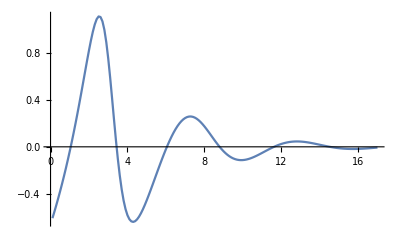

InterpolatingFunction[{{0.1, 17.}}, <>]

```mathematica
dots=Transpose[{StepE,-Im[c]}];
ListLinePlot[dots]
iFun=Interpolation[dots]
```

```mathematica
s$rule=FindRoot[iFun[x],{x, 11},WorkingPrecision->18];
x$sol=x/.s$rule
```

11.6206954696438666

```mathematica
1.06036386484119794359253009378234334463`18.
```

1.06036386484119794

```mathematica
1.4771499462953836149950773530013772389`20. 320
```

```mathematica
1.47715081118640185469496608175679527779`18.
```